```mathematica
m={{30,0},{30,2},{10,39},{10,42},{25,13},{15,29}};
```

```mathematica
m={{4,0},{2,29},{1,35},{1,44}};
```

```mathematica
m={{50,505},{100,0},{100,0}};
```

```mathematica
m={{5,10},{100,0}};
```

```mathematica
g[y_]:=Flatten[Map[{#,#+5}&,Map[#[[1]]*x+#[[2]]&,y]]];
```

```mathematica
f[x_]:=Table[i->{i+1},{i,1,Length[x]*2,2}]
```

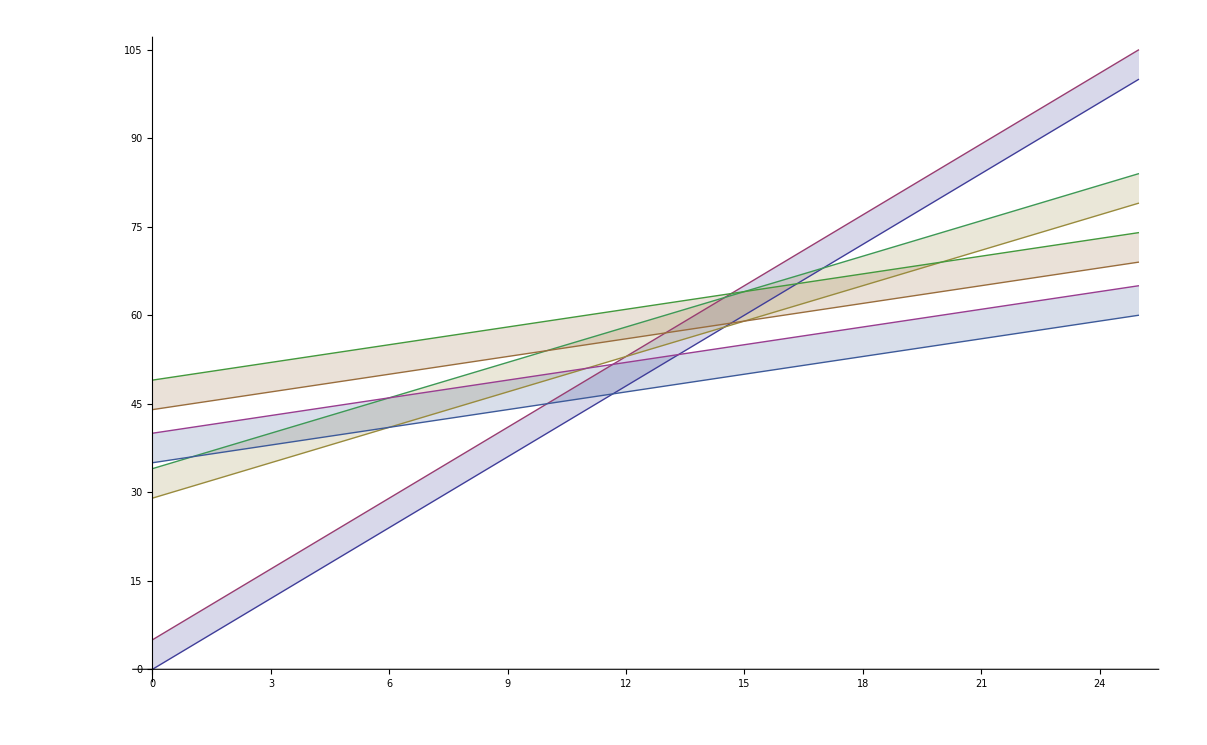

```mathematica
Plot[Evaluate[g[m]], {x, 0, 25},Filling->f[m]]
```

```mathematica
i=.;j=.;D2=.;
```

```mathematica
Solve[{-y+Si*x+pi+D1==0,-y+Sj*x+pj+D2==0},{x,y}]
```

{{x→-(D1-D2+pi-pj)/(Si-Sj),y→-(-D2 Si-pj Si+D1 Sj+pi Sj)/(Si-Sj)}}

```mathematica
t[i_,p_]:=-y+m[[i,1]]*x+m[[i,2]]+p==0;
```

```mathematica
Solve[{t[1,5],t[2,0]},{x,y}]//N
```

{{x→10.2,y→1020.}}

```mathematica
p={};
For[i=1,i<=Length[m],i++,
For[j=1+i,j<=Length[m],j++,
If[m[[i,1]]≠m[[j,1]],
AppendTo[p,{

{x,y}/.Solve[{l[i],u[j]},{x,y}][[1]],
{x,y}/.Solve[{u[i],u[j]},{x,y}][[1]],
{x,y}/.Solve[{u[i],l[j]},{x,y}][[1]],
{x,y}/.Solve[{l[i],l[j]},{x,y}][[1]]}]
]]
]
```

```mathematica
p
```

{{{17,68},{29/2,63},{12,53},{29/2,58}},{{40/3,160/3},{35/3,155/3},{10,45},{35/3,140/3}},{{49/3,196/3},{44/3,191/3},{13,57},{44/3,176/3}},{{11,51},{6,46},{1,36},{6,41}},{{20,69},{15,64},{10,54},{15,59}}}

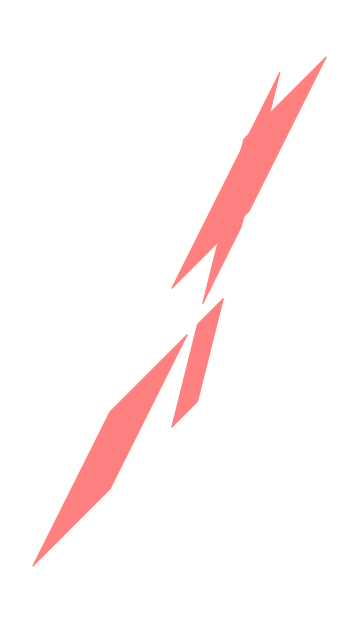

```mathematica
Graphics[{EdgeForm[Dashed],Pink,Polygon[p]}]
```

```mathematica
<<Imtek`Geometry`Polygon`
```

Get::noopen: Cannot open "Imtek`Geometry`Polygon`".

$Failed